```mathematica
f[x_]=Sqrt[x];
a=0;
b=1;
```

```mathematica
p=ParametricPlot3D[{x,f[x]Cos[r],f[x]Sin[r]},{x,a,b},{r,0,2 Pi}]
```

-Graphics3D-

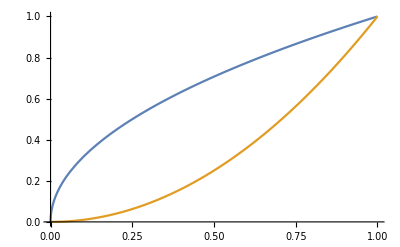

-Graphics3D-

```mathematica
g[x_]=x^2;
Plot[{f[x],g[x]},{x,0,1}]
q=ParametricPlot3D[{x,g[x]Cos[r],g[x]Sin[r]},{x,a,b},{r,0,2 Pi}]
```

```mathematica
Show[p,q]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[x^2,{x,0,1}](*Y axis rotation*)
```

-Graphics3D-